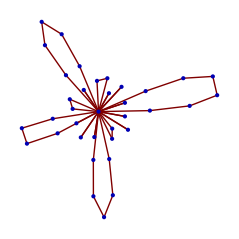

```mathematica
With [{tuple={3,5,7,11,13,17}},    
With [{votes=VoteList[0,10,tuple]},
GraphPlot[
Select[Sort[Table[ {votes[[pos-1]][[2]][[1]]-> votes[[pos]][[2]][[1]],votes[[pos]] [[1]]}, {pos,2, Length[ votes]}]],  # [[1]][[1]]≠0 || # [[1]][[2]]≠0&]
,
VertexLabeling->False,
EdgeLabeling->False,
DirectedEdges->False,
MultiedgeStyle->None,
ImageSize->Large
]
]
]
```

```mathematica
With [{tuple={7,11,13,17}},    
With [{votes=VoteList[0,20,tuple]},

Sort[Table[ {votes[[pos-1]][[2]][[4]]-> votes[[pos]][[2]][[4]],pos }, {pos,2, Length[ votes]}]]
]
]
```

{{0→0,2},{0→0,3},{0→0,4},{0→0,5},{0→0,8},{0→0,12},{0→0,13},{0→0,14},{0→0,15},{0→0,16},{0→0,21},{0→0,22},{0→0,23},{0→0,24},{0→0,27},{0→0,28},{0→0,29},{0→0,32},{0→0,33},{0→0,34},{0→0,38},{0→0,43},{0→0,46},{0→0,47},{0→0,53},{0→0,54},{0→0,57},{0→0,67},{0→0,68},{0→0,69},{0→0,70},{0→0,91},{0→0,113},{0→0,114},{0→0,115},{0→0,118},{0→0,119},{0→0,120},{0→0,133},{0→0,138},{0→0,177},{0→0,178},{0→0,179},{0→0,182},{0→0,185},{0→0,186},{0→0,187},{0→0,188},{0→0,225},{0→0,226},{0→0,227},{0→0,228},{0→0,231},{0→0,232},{0→0,236},{0→0,268},{0→0,291},{0→0,292},{0→0,293},{0→0,296},{0→0,297},{0→0,298},{0→0,306},{0→0,307},{0→0,308},{0→0,311},{0→0,312},{0→0,313},{0→0,314},{0→0,315},{0→0,359},{0→0,365},{0→0,368},{0→0,369},{0→0,386},{0→0,389},{0→0,390},{0→0,391},{0→0,396},{0→0,397},{0→0,476},{0→0,579},{0→0,580},{0→0,581},{0→0,582},{0→0,585},{0→0,588},{0→0,589},{0→0,603},{0→0,606},{0→0,607},{0→0,608},{0→0,609},{0→0,612},{0→0,613},{0→0,614},{0→0,615},{0→0,625},{0→0,626},{0→0,678},{0→0,686},{0→0,692},{0→0,693},{0→0,696},{0→0,697},{0→0,698},{0→0,699},{0→0,700},{0→0,703},{0→0,704},{0→0,707},{0→0,708},{0→0,709},{0→1,172},{0→1,360},{0→1,405},{0→1,408},{0→2,304},{0→2,384},{0→3,17},{0→3,44},{0→3,111},{0→4,6},{0→4,55},{0→4,95},{0→4,125},{0→4,134},{0→4,623},{0→5,30},{0→5,51},{0→5,223},{0→5,289},{0→5,586},{0→5,701},{0→6,180},{0→6,229},{0→6,299},{0→6,387},{0→6,444},{0→6,616},{0→6,716},{0→7,35},{0→7,116},{0→7,183},{0→7,221},{0→7,233},{0→7,366},{0→7,594},{0→7,604},{0→7,705},{0→8,9},{0→8,25},{0→8,58},{0→8,71},{0→8,121},{0→8,189},{0→8,294},{0→8,309},{0→8,370},{0→8,394},{0→8,583},{0→8,610},{0→8,636},{0→8,710},{0→28,175},{0→39,200},{0→50,592},{0→51,402},{0→56,48},{0→56,73},{0→58,560},{0→65,675},{0→78,316},{0→82,170},{0→96,136},{0→98,60},{0→99,712},{0→103,577},{0→104,244},{0→106,64},{0→107,372},{0→109,642},{0→113,237},{0→114,39},{0→120,19},{0→124,191},{0→124,442},{0→127,618},{0→130,681},{0→132,302},{0→133,601},{0→136,679},{0→140,129},{0→143,590},{0→143,690},{0→144,392},{0→144,627},{0→469,574},{0→495,633},{0→582,105},{0→736,326},{0→996,439},{0→1108,683},{0→1510,437},{0→1560,139},{0→1623,596},{0→1684,673},{0→1693,382},{0→1696,687},{0→1755,414},{0→1880,108},{0→1956,599},{0→1959,400},{0→2032,88},{0→2181,97},{0→2251,41},{0→2347,569},{0→2378,694},{0→2403,99},{0→2438,398},{0→4471,92},{0→4659,465},{0→5991,77},{0→15265,81},{0→19537,629},{0→19563,411},{0→23847,247},{0→25332,671},{0→25817,474},{0→27253,471},{0→29929,215},{0→31879,722},{0→31925,454},{0→32247,320},{0→33772,380},{0→35029,158},{0→35615,141},{0→35675,649},{0→35819,503},{0→36479,647},{0→36939,84},{0→41343,551},{0→75534,477},{0→117169,492},{0→137436,198},{0→197398,205},{0→244664,469},{0→313853,546},{0→323716,482},{0→380425,357},{0→388726,724},{0→515333,463},{0→569972,543},{0→596314,86},{0→664300,329},{0→686646,212},{0→689986,553},{0→706427,435},{0→1637237,353},{0→2725399,333},{0→4877334,251},{0→4902574,496},{0→4946625,161},{0→6181933,767},{0→6357956,279},{0→7921531,148},{0→8074380,417},{0→10034210,242},{0→10078261,156},{0→10457394,555},{0→10823923,511},{0→19786500,255},{0→35207607,490},{0→42069606,426},{0→50588237,664},{0→58421660,654},{0→65428112,727},{0→88344275,525},{0→89980725,269},{0→110227681,258},{0→140850033,480},{0→160494098,751},{0→187479992,324},{0→189605587,488},{0→330683043,263},{0→961551223,780},{0→3065289086,261},{0→3359871216,450},{0→3437320488,749},{0→3481006379,351},{0→8865218359,500},{0→17358542982,792},{0→19222779459,517},{0→20455303097,771},{0→33304186133,277},{0→35839323240,732},{0→38534397005,348},{0→50625958592,778},{0→52630387151,662},{0→58837647047,275},{0→66270470455,538},{0→223833506412,341},{0→317086306753,534},{0→530033302791,530},{0→629952356744,758},{0→8783213184006,536},{0→10557333949396,786},{0→11675069035518,741},{0→15905925042779,824},{0→16492993478337,660},{0→1678904779614684,835},{0→4059650523014718,790},{0→4074514349833175,805},{0→4388063170924159,798},{0→74100737585643290,811},{0→164928789527400105,816},{0→1413270217998208201,831},{0→21292444535585952138,833},{1→0,104},{1→3,361},{1→4,173},{1→4,621},{1→124,123},{1→143,406},{1→2011,639},{1→11414195,409},{2→0,11},{2→0,305},{2→0,385},{2→0,689},{2→36283,714},{3→0,18},{3→0,45},{3→0,112},{3→26,362},{3→1660,131},{4→0,7},{4→0,56},{4→0,96},{4→0,135},{4→0,174},{4→0,364},{4→0,622},{4→0,624},{4→28,126},{4→9787530,196},{4→21698866090,265},{5→0,31},{5→0,52},{5→0,224},{5→0,290},{5→0,587},{5→0,702},{5→1,620},{5→68354,447},{6→0,181},{6→0,230},{6→0,388},{6→0,617},{6→137,300},{6→1791,717},{6→369364,445},{7→0,117},{7→0,184},{7→0,222},{7→0,367},{7→0,404},{7→0,595},{7→0,605},{7→0,706},{7→76,234},{7→137,36},{8→0,26},{8→0,59},{8→0,72},{8→0,190},{8→0,295},{8→0,310},{8→0,371},{8→0,395},{8→0,584},{8→0,611},{8→0,711},{8→1,122},{8→2,10},{8→1913,637},{10→0,441},{12→688380,720},{13→1384,433},{22→0,50},{26→4,363},{28→0,176},{28→1963,127},{29→0,110},{38→19344215,562},{39→21414,201},{41→0,598},{41→2409,318},{45→0,641},{50→0,593},{51→7,403},{51→127,644},{56→22,49},{56→1955,74},{58→38,561},{65→135,676},{68→78814143,338},{70→17075,240},{76→0,235},{78→41,317},{82→0,171},{96→0,137},{98→917,61},{99→2,713},{103→0,578},{104→591681,245},{105→444292,631},{106→110,65},{107→35032,373},{109→51,643},{110→0,66},{113→34396,238},{114→0,40},{120→0,20},{123→30012,431},{124→0,124},{124→0,443},{124→2062,192},{127→5,619},{127→2188,645},{130→0,682},{132→0,94},{132→0,303},{133→0,602},{135→0,677},{136→0,680},{137→0,37},{137→0,301},{140→3,130},{142→369085,101},{143→0,407},{143→0,591},{143→0,691},{144→0,393},{144→0,628},{184→68,337},{265→600876,669},{407→955,167},{469→13999,575},{495→12242,634},{582→13413,106},{589→1176,79},{649→0,90},{674→21354,283},{736→8351617,327},{777→0,63},{875→1523,375},{917→777,62},{955→236350,168},{996→10,440},{1108→2448,684},{1176→0,80},{1209→4650398,146},{1262→2320,549},{1263→0,288},{1286→208217,485},{1384→0,434},{1510→0,438},{1523→25703,376},{1560→0,140},{1623→41,597},{1660→0,132},{1684→0,674},{1693→0,383},{1696→2,688},{1755→5812477,415},{1791→33638,718},{1810→21590,217},{1880→29,109},{1913→1,638},{1955→39598,75},{1956→0,600},{1959→0,401},{1963→0,128},{1965→1263,287},{2011→45,640},{2017→2042,571},{2032→649,89},{2042→22262,572},{2062→22711,193},{2073→2372,219},{2095→0,83},{2099→38733,285},{2181→0,98},{2188→0,646},{2251→0,42},{2319→8181,153},{2320→0,550},{2347→2017,570},{2372→0,220},{2378→0,695},{2403→142,100},{2409→0,319},{2438→0,399},{2448→0,685},{4471→132,93},{4659→307040780,466},{5891→11633280,331},{5991→589,78},{8181→508196,154},{9824→523231,378},{12242→0,635},{13041→21482,143},{13413→0,107},{13999→0,576},{15265→2095,82},{16706→314596,203},{17075→0,241},{17409→1,103},{17756→663206,322},{19537→105,630},{19563→629625,412},{21027→407,166},{21354→2099,284},{21414→16706,202},{21482→285381,144},{21590→2073,218},{22262→0,573},{22711→415769,194},{22804→2443498,567},{22948→159221614,208},{23847→239977,248},{25332→0,672},{25703→9824,377},{25817→0,475},{27253→528309,472},{29929→1810,216},{30012→13,432},{31879→0,723},{31925→706660,455},{32247→17756,321},{33638→12,719},{33772→0,381},{34396→70,239},{35029→195979792,159},{35032→875,374},{35615→13041,142},{35675→92588,650},{35819→26143871636,504},{36283→0,715},{36479→0,648},{36939→0,85},{37102→6946958,459},{38733→1965,286},{39468→1262,548},{39598→0,76},{40325→674,282},{41343→0,552},{54768→123,430},{68354→132299099,448},{75534→10512610,478},{77689→3319537857,747},{92588→10054898,651},{117169→563951,493},{137436→0,199},{150588→301522,461},{197398→10631381,206},{201395→390708,565},{208217→7212207,486},{224635→295953,151},{236350→0,169},{239977→655162,249},{244664→0,470},{265586→16601401798,421},{285381→1209,145},{295953→2319,152},{301522→0,462},{313670→202628284,253},{313853→39468,547},{314596→0,204},{323716→626981,483},{369085→17409,102},{369364→5,446},{380425→0,358},{388726→187995241,725},{390708→22804,566},{412245→5310699,164},{415707→265586,420},{415769→4,195},{444292→0,632},{508196→0,155},{515333→0,464},{523231→0,379},{528309→0,473},{563951→45100857,494},{569972→5806996,544},{591681→0,246},{596314→0,87},{600876→0,670},{618488→40325,281},{619264→4982131,557},{626981→1286,484},{629625→0,413},{655162→0,250},{663206→0,323},{664300→5891,330},{686646→10030686,213},{688380→0,721},{689986→0,554},{706427→0,436},{706660→1358965,456},{965201→128320684148,775},{1358965→84702180,457},{1633488→52166255304,541},{1637237→196919368,354},{2443498→0,568},{2725399→11235559,334},{3189196→265,668},{4650398→0,147},{4877334→313670,252},{4902574→7674218,497},{4946625→11516960,162},{4982131→178757301,558},{5310699→21027,165},{5806996→0,545},{5812477→0,416},{6181933→30548849144,768},{6357956→618488,280},{6583862→0,356},{6946958→150588,460},{7212207→0,487},{7674218→59217238571,498},{7921531→9664190,149},{8074380→3461249663,418},{8351617→0,328},{8410860→38944950,666},{9664190→224635,150},{9787530→0,197},{10030686→0,214},{10034210→0,243},{10054898→196944918,652},{10078261→0,157},{10457394→619264,556},{10512610→0,479},{10631381→22948,207},{10823923→11594321,512},{11235559→2083153410,335},{11414195→0,410},{11516960→412245,163},{11594321→45907272623,513},{11633280→0,332},{19344215→53475035,563},{19786500→3021103955,256},{19994035→44982029,271},{31881848→77689,746},{35207607→0,491},{38944950→3189196,667},{42069606→340742347,427},{44982029→694384470,272},{45100857→0,495},{50588237→8410860,665},{53475035→201395,564},{58421660→3406137946,655},{65428112→3015400008,728},{72641657→56811875576,452},{74366622→104084347,210},{78814143→57925064644,339},{84702180→37102,458},{88344275→437220613637,526},{89980725→19994035,270},{104084347→0,211},{110227681→1965605163,259},{132299099→0,449},{140850033→0,481},{155830270→2917314376,730},{159221614→74366622,209},{160494098→372272128,752},{178757301→0,559},{187479992→0,325},{187995241→0,726},{189605587→0,489},{190802850→54768,429},{195979792→0,160},{196919368→6583862,355},{196944918→0,653},{202628284→0,254},{307040780→1892479259,467},{311431578→38283221825,424},{330683043→4,264},{340742347→190802850,428},{372272128→23056754373,753},{694384470→2314781301,273},{934294734→385329604602,523},{961551223→46729227259,781},{1143865895→2860484265,755},{1471715325→31881848,745},{1625534660→941017688460,658},{1656656971→0,267},{1679296246→1633488,540},{1880767136→140979274909038,734},{1892479259→0,468},{1965605163→0,260},{2024491609→16189394108847750,813},{2083153410→184,336},{2094578481→965201,774},{2314781301→0,274},{2860484265→362513952897,756},{2917314376→0,731},{2929307378→8300700899,344},{3015400008→155830270,729},{3021103955→0,257},{3065289086→0,262},{3218025642→0,777},{3272750072→9623348432975,521},{3319537857→0,748},{3359871216→72641657,451},{3406137946→32895639952,656},{3437320488→0,750},{3461249663→415707,419},{3481006379→0,352},{8300700899→895334025648,345},{8865218359→908238511346,501},{15476267405→55642281511,763},{16601401798→10973811185152,422},{17358542982→263253412224467,793},{18071811391→265457000697889,826},{19222779459→163052699486,518},{20455303097→580378088345,772},{21698866090→1656656971,266},{23056754373→1143865895,754},{23748148015→0,770},{26143871636→184993483689,505},{30548849144→23748148015,769},{32895639952→1625534660,657},{33304186133→0,278},{35839323240→1880767136,733},{38283221825→0,425},{38534397005→58515472140,349},{39754967783→810180965721,760},{43801417846→1471715325,744},{45907272623→981363298975,514},{46729227259→1003067902153,782},{48716138183→4942085901817484,739},{49798225426→3272750072,520},{50625958592→0,779},{52166255304→0,542},{52630387151→0,663},{55642281511→7756486965957,764},{56811875576→0,453},{57891125552→391927751581,509},{57925064644→0,340},{58515472140→0,350},{58837647047→0,276},{59217238571→0,499},{66270470455→1679296246,539},{105738993461→0,766},{128320684148→3218025642,776},{163052699486→49798225426,519},{184993483689→2077931476064,506},{223833506412→893559424177,342},{317086306753→0,535},{362513952897→0,757},{385329604602→0,524},{391927751581→0,510},{421225617468→48716138183,738},{437220613637→7272760166224,527},{530033302791→256619154682763,531},{580378088345→2094578481,773},{584846482359→0,347},{629952356744→39754967783,759},{646784057974→0,516},{665531148272→57891125552,508},{690585475820→109067280871068,784},{810180965721→8007302802255,761},{893559424177→2929307378,343},{895334025648→584846482359,346},{908238511346→0,502},{941017688460→0,659},{981363298975→646784057974,515},{1003067902153→690585475820,783},{2077931476064→665531148272,507},{3492617748891→257733368269051,788},{3923180115575→15640378260172,736},{7272760166224→202872403646520,528},{7756486965957→105738993461,765},{8007302802255→15476267405,762},{8783213184006→0,537},{9623348432975→934294734,522},{10557333949396→3492617748891,787},{10973811185152→311431578,423},{11675069035518→285944710807789,742},{15640378260172→421225617468,737},{15905925042779→18071811391,825},{16340043077065→329857579054800210,818},{16492993478337→0,661},{26980202865256→66006040531219415,796},{48987672189500→2379406326722321,821},{73585566803806→145123732650861,808},{80940608595768→80826188048348073,801},{109067280871068→0,785},{119453113778834→0,533},{122502944607083→189933881912282,828},{140979274909038→3923180115575,735},{145123732650861→1915165418690980,809},{189933881912282→4668037926742359,829},{202872403646520→0,529},{256619154682763→119453113778834,532},{257733368269051→0,789},{263253412224467→3573160300957524,794},{265457000697889→122502944607083,827},{269073416138777→8094697054423875,803},{285944710807789→43801417846,743},{1915165418690980→0,810},{2379406326722321→3572329004019663,822},{3252566634661649→80940608595768,800},{3572329004019663→0,823},{3573160300957524→26980202865256,795},{4059650523014718→0,791},{4074514349833175→4903799723625392,806},{4388063170924159→3252566634661649,799},{4668037926742359→0,830},{4903799723625392→73585566803806,807},{4942085901817484→0,740},{8094697054423875→0,804},{16189394108847750→1346081966011934480,814},{56984713409100883→48987672189500,820},{66006040531219415→0,797},{74100737585643290→2024491609,812},{80826188048348073→269073416138777,802},{164928789527400105→16340043077065,817},{329857579054800210→56984713409100883,819},{1346081966011934480→0,815},{1413270217998208201→0,832},{21292444535585952138→0,834}}

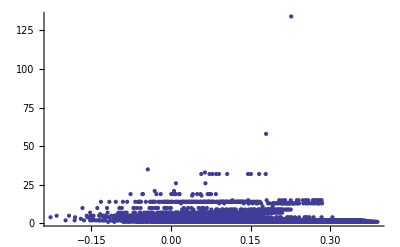

```mathematica
ListPlot[Sort[Table[{magicGraham [l],  FiniteGroupCount[Product[a, {a,l}]]} , {l, Subsets[Table[Prime[p],{p,2,25}], {4}]}]],  PlotRange->All]
```